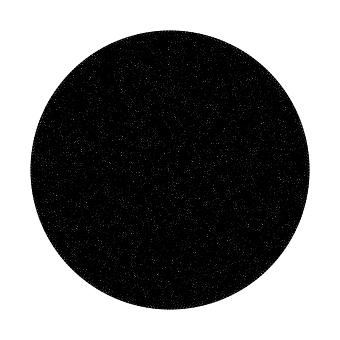

Number of Elements:21402

```mathematica
Needs["NDSolve`FEM`"]
R=10;
maxCellMeasure=0.025;
Ω=Disk[{0,0},R];
mesh=ToElementMesh[Ω,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure,MeshQualityGoal-> 1,"NodeReordering"-> True,"IncludePoints"->{{0.,0.}}];
coorVerticesXY=mesh["Coordinates"];
coorVerticesXYZ=MapThread[Append,{coorVerticesXY,ConstantArray[0,Length[coorVerticesXY]]}];
conn=mesh["MeshElements"][[1]][[1]];
Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXY,Polygon[conn]]}]]
numberElements=Dimensions[conn,1][[1]];
Labeled["Number of Elements:",numberElements]
```

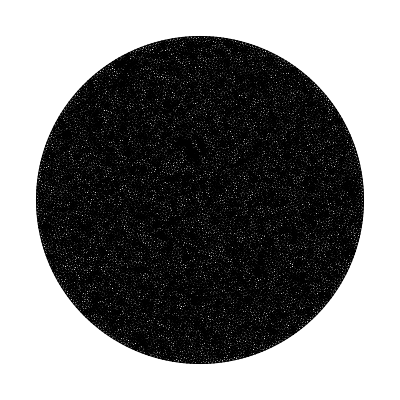

```mathematica
mm=Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXY,Polygon[conn]]}]]
```

```mathematica
Export[NotebookDirectory[]<>"CircleMesh-7.obj",mm,"Binary"-> True]
```

/Users/bricelecampion/Documents/Work/Geomechanics/Codes/minimalFE/mma-stuff/CircleMesh-7.obj

```mathematica
665*3
```

1995

```mathematica
(Norm[#]&/@ mesh[[1]] )// Min
```

0.11355

```mathematica
mesh[[1]]//Length
```

134624

```mathematica
90/15
```

6

```mathematica
56/11
```

```mathematica
66/8
```

33/4

## including a fracture in a square Mesh

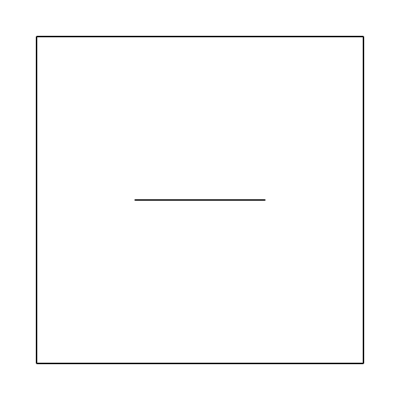

```mathematica
bmesh=ToBoundaryMesh["Coordinates"->{{0,0},{1,0},{1,1},{0,1},{0.3,0.5},{0.7,0.5}},"BoundaryElements"->{LineElement[{{1,2},{2,3},{3,4},{4,1}}],LineElement[{{5,6}}]}];
bmesh["Wireframe"]
```

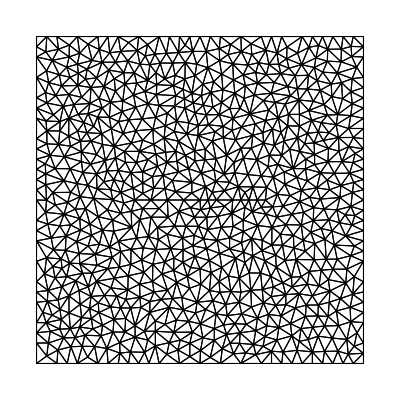

```mathematica
mesh=ToElementMesh[bmesh,MaxCellMeasure->0.001];
mesh["Wireframe"]
```

```mathematica
mesh[[1]]
```

{{0.,0.},{1.,0.},{1.,1.},{0.,1.},{0.3,0.5},{0.7,0.5},{0.5,0.},{0.5,1.},{0.5,0.29},{0.5,0.5},{0.4,0.395},{0.4,0.5},{0.35,0.4475},{0.402562,0.4475},{0.35,0.5},{0.325,0.47375},3246,{0.858641,0.953528},{0.822823,0.983517},{0.828125,1.},{0.859375,1.},{0.15625,0.},{0.171875,0.00972569},{0.203125,0.},{0.91956,0.813104},{0.934462,0.83455},{0.963744,0.812877},{0.950824,0.802265},{0.928672,0.785603},{0.947382,0.845162},{0.948904,0.820578},{1.,0.765625},{0.980513,0.769641}}
 |  |  |  |